```mathematica
SetDirectory[NotebookDirectory[]];
vmax=20;
rBar=4;
Lf=vmax*Max[1,1/rBar^2+1/rBar];
sigma=0.48;
lr=2;
Lh=1/rBar^2;
rmin[xi_,off_]:=rBar/(sigma*Cos[xi/2]+1-sigma)+off;
h[xi_,off_]:=(sigma*Cos[xi/2]+1-sigma)/rBar-1/rmin[xi,off];
f[xi_,beta_,off_]:={vmax*Cos[xi-beta],-vmax/rmin[xi,off]*Sin[xi-beta]-vmax/lr*Sin[beta]};
deltaFMax=Pi/4;
betaMax=ArcTan[0.5*Tan[deltaFMax]];
```

## Solution for Cloud Wait Time (aka “Δt”)

Recall from our prior calculations that we are interested in solutions for t of the following equation:

Sqrt[2]*Lh*Norm[f[ξ, β0, offset]]*t*Exp[Lf*t] == h[ξ, offset]

This equation can be solved numerically to any desired accuracy for any particular choice of ξ and β_0 (and offset although we will focus on the others -- see note below); however, we need to be able to determine a wait-time value for any possible (real-valued) values for ξ and β_0. Thus, we use analytical information about the functions (equation) in question to construct a lookup table whose elements are spaced finely enough that we can bound the difference between any real-valued (ξ,β_0) and the nearest point stored in the lookup table.

Note: we have parameterized this equation by r_min[ξ]+offset for the usual technical reasons. In particular, the value of h[ξ,r_min[ξ]+offset] increases in the variable offset for each ξ (I believe this needs to be shown still -- the analogous result in the paper is for the more complicated ZBF).

## Using the Implicit Function Theorem to Bound the Derivative of the Solution of (1)

The obvious approach to determine a grid size for the lookup table is to bound the Lipschitz constant of the function in question. In particular, we will consider that (1) defines an implicit function of ξ and β_0 for each value of offset. We denote this function by:

t̃:(ξ,β_0)∈[-π,π]×[-β_max,β_max]→ℝ

i.e. t̃[ξ,β_0] solves (1) above. Define the following set for convenience:

D=[-π,π]×[-β_max,β_max]

We can rewrite (1) as an equation with zero as a right-hand side, and specify this in Mathematica as follows:

```mathematica
F=Evaluate[Sqrt[2]*Lh*Norm[f[ξ,β0,offset]]*t*Exp[Lf*t]-h[ξ,offset]]
```

(ⅇ^(20 t) t √(400 Abs[Cos[β0-ξ]]^2+Abs[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2))/(8 √2)+1/(offset+4/(0.52+0.48 Cos[ξ/2]))+1/4 (-0.52-0.48 Cos[ξ/2])

Now the implicit function theorem says (in part) that the gradient of t̃[ξ,β_0] with respect to (ξ,β_0) can be expressed in terms of the implicit function, t̃:

(∂t̃)/(∂(ξ,β_0))[ξ,β_0]=-((∂F)/(∂t)[ξ,β_0,t̃[ξ,β_0]])^-1*(∂F)/(∂(ξ,β_0))[ξ,β_0,t̃[ξ,β_0]]

provided the gradient ∂F/∂t is invertible. Since we are interested in bounding the Lipschitz constant of t̃, we can apply the Mean-Value Theorem (MVT) if we are able to bound the gradient in (3).

We can have Mathematica compute the appropriate expressions as follows. Let:

dF_den[ξ,β_0]=(∂F)/(∂t)[ξ,β_0,t̃[ξ,β_0]]
dF_num[ξ,β_0]=(∂F)/(∂(ξ,β_0))[ξ,β_0,t̃[ξ,β_0]]

then compute:

```mathematica
dFnum=D[F,{{ξ,β0}}]; (* Surpressed output for convenience *)
```

```mathematica
dFden=Simplify[D[F,t]]
```

(5 ⅇ^(20 t) (1+20 t) √(4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2))/(4 √2)

In particular, we can upper-bound the expression in (3) by upper-bounding the numerator, dF_num, and simultaneously lower-bounding the denominator, dF_den. The numerator is generally no problem; we skip that for later. Clearly, a lower bound for the denominator can be obtained by separately lower-bounding the two factors in the expression above. The first, ⅇ^(5 t) (1+5 t), is clearly lower-bounded by 1, since any solution for t of (1) is non-negative. Thus, we have to consider a lower bound for the other expression, extracted here:

```mathematica
lowerBoundQty[ξ_,β0_,offset_]:=Evaluate[Reap[Simplify[D[F,t]]/.Sqrt[x_]:>Sow[x]]⟦2⟧//Flatten//First]
lowerBoundQty[ξ,β0,offset]
```

4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2

(noting that √is monotonic, so can be omitted from determining the (ξ^*,β_0^*) of the minimum).

However, it is unfortunately the case that the minimum of lowerBoundQty[ξ,β0,offset] is zero on the region of interest (note the particular choice of offset 5):

```mathematica
offs=5;
```

```mathematica
badMin=FindMinimum[
lowerBoundQty[ξ,β0,offs],
{{ξ,-Pi/2},{β0,0}}
]
```

{1.01819×10^-16,{ξ→-1.35815,β0→0.212643}}

This is obviously unacceptable, since it creates a trivial lower-bound on dF_den of 0, and hence a trivial upper-bound on the quantity of ultimate interest, (∂t̃)/(∂(ξ,β_0))[ξ,β_0], viz. +∞.

Note: this means that there is NO finite grid-size over the ENTIRE REGION [-π,π]×[-β_max,β_max] that will create a finite upper-bound on the error between t̃[ξ,β_0] and any grid point!

## Bounding the denominator of Implicit Function Gradient (old method)

Thus, we take the following approach. We will split the set [-π,π]×[-β_max,β_max] into two subsets: one on which lowerBoundQty is bounded below by a small -- but finite -- value, and the other on which lowerBoundQty can reach zero, but on which every solution t̃[ξ,β_0] is larger than some fixed value. Formally, we wish to choose some set S_offset⊂[-π,π]×[-β_max,β_max]=D such that the following hold:

∀(ξ,β_0)∈D\S_offset . lowerBoundQty[ξ,β_0,offset]>=δ_offset

∀(ξ,β_0)∈S_offset . t̃[ξ,β_0,offset]>=T_offset

for some constants δ_offset and T_offset (functions of only offset).

One natural way to obtain such a set is to solve (1) using instead an upper-bound on its left-hand side. This will immediately give us a set of points (in the ξ-β_0 plane) for which (7) is true. In particular, let’s consider upper-bounding the t factor in (1) by Exp[t]. Thus, we can define a set S_offset as follows for a particular choice of T_offset:

S_offset={(ξ,β_0)∈D: 1/(2*Lf)*Log[h[ξ,offset]/(Sqrt[2]*Lh*Norm[f[ξ,β0,offset]])]>=T_max}

This choice comes with the assurance that ∀(ξ,β_0)∈S_offset. t̃[ξ,β_0]>=T_max. Thus, if we are lucky, we can prove that (6) holds for this set as well.

This seems likely to be the case, given the following observation. Consider the following plot, which shows the upper-bound expression used in (8) with the actual numerical solutions to (1). In particular, the output range of the plot is limited to [0,0.25], and the input range is set to a small interval around (one of) the points at which lowerBoundQty is zero, viz. {ξ→-1.53857,β0→0.0322252} from the numerical minimization above. (The orange surface is the numerical solution to (1); the blue surface is a plot of the expression in (8).)

```mathematica
Tmax[offs]=0.075
```

0.075

```mathematica
numPoints=40;
rng={{ξ-0.1,ξ+0.1},{β0-0.1,β0+0.1}}/.badMin⟦2⟧;
data=Flatten[ParallelTable[
{xi,beta,t/.Flatten@Quiet@NSolve[Sqrt[2]*2*Lh*Norm[f[xi,beta,offs]]*t*Exp[Lf*t]==h[xi,offs],t]},
{xi,rng⟦1,1⟧,rng⟦1,2⟧,(rng⟦1,2⟧-rng⟦1,1⟧)/numPoints},
{beta,rng⟦2,1⟧,rng⟦2,2⟧,(rng⟦2,2⟧-rng⟦2,1⟧)/(2*numPoints)}
],1];
Show[
ListPlot3D[
data,
AxesLabel->(Style[#,FontSize->16]&/@{"ξ","β","Δt"}),
PlotRange->{0,Tmax[offs]}
],
Plot3D[
Log[h[ξ,offs]/(Sqrt[2]*Lh*Norm[f[ξ,β0,offs]])]/(2*Lf),
{ξ,rng⟦1,1⟧,rng⟦1,2⟧},
{β0,rng⟦2,1⟧,rng⟦2,2⟧},
PlotRange->{0,0.25},
PlotPoints->50,
PlotTheme->"CoolColor",
PlotStyle->{Directive[Opacity[0.5]]}
],
PlotRange->{rng⟦1⟧,rng⟦2⟧,{0,Tmax[offs]}}
]
```

-Graphics3D-

-Graphics3D-

As expected, the blue surface is always less-than the orange one, so that the super-level set in (8) is guaranteed to be contained within the super-level set of the actual numerical solution to (1), viz. {(ξ,β_0):t̃[ξ,β_0]>=T_offset=0.25}. However, we note further that the solution of (1) for the problematic point of lowerBoundQty is well within this set:

```mathematica
FindMinimum[
Evaluate[F/.badMin⟦2⟧/.offset->offs]^2,
{{t,1}}
]
```

{2.55178×10^-29,{t→0.829205}}

This is clearly larger than the choice T_offset=0.2 for offset=5.

So it is very likely that (6) holds for this choice of S_offset for some finite value δ_offset.

This is the subject of the next subsection, although here we will do things a little bit sloppily (i.e. numerically).

### Finding a lower bound for the denominator on D\S_offset

We will proceed with this objective -- i.e. “proving” (6) holds for our choice of S_offset -- using numerical optimization on a Lagrangian. First, though, we should convince ourselves that the minima of the denominator appear only on the boundary of the set S_offset. For now, we will do this just by inspection since time is short.

```mathematica
Plot3D[
lowerBoundQty[ξ,β0,offs],
{ξ,rng⟦1,1⟧,rng⟦1,2⟧},
{β0,rng⟦2,1⟧,rng⟦2,2⟧},
PlotRange->{0,1}
]
```

-Graphics3D-

```mathematica
Plot3D[
lowerBoundQty[ξ,β0,offs],
{ξ,-Pi,Pi},
{β0,-Pi/4,Pi/4},
PlotRange->{0,5}
]
```

-Graphics3D-

```mathematica
optimPlotRange={{ξ-0.02,ξ+0.02},{β0-0.02,β0+0.02}}/.badMin⟦2⟧;
ListPlot3D[
Flatten[Table[
If[
(Log[h[ξ,offs]/(Sqrt[2]*Lh*Norm[f[ξ,β0,offs]])]/(2*Lf))>=Tmax[offs],
{ξ,β0,lowerBoundQty[ξ,β0,offs]},
{ξ,β0,0}
],
{ξ,optimPlotRange⟦1,1⟧,optimPlotRange⟦1,2⟧,(optimPlotRange⟦1,2⟧-optimPlotRange⟦1,1⟧)/250},
{β0,optimPlotRange⟦2,1⟧,optimPlotRange⟦2,2⟧,(optimPlotRange⟦2,2⟧-optimPlotRange⟦2,1⟧)/250}
],1],
PlotRange->{0,0.0001}
]
```

-Graphics3D-

```mathematica
Dimensions[%]
```

{2}

Together, these suggest that the minimum of lowerBoundQty over the set D\S_offset is indeed likely to be on the boundary of S_offset. Thus, we proceed under this assumption, and use a single Lagrange multiplier to account for this equality constraint, viz:

```mathematica
L[ξ_,β0_,offset_,λ_,Toff_]:=lowerBoundQty[ξ,β0,offset]+λ*(Sqrt[2]*Lh*Norm[f[ξ,β0,offset]]*ⅇ^(2*Lf*Toff)-h[ξ,offset])
constraint[ξ_,β0_,offset_,Toff_]:=Sqrt[2]*Lh*Norm[f[ξ,β0,offset]]*ⅇ^(2*Lf*Toff)-h[ξ,offset]
```

```mathematica
Norm[f[ξ,β0,offset]]
```

√(400 Abs[Cos[β0-ξ]]^2+Abs[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2)

```mathematica
lowerBoundQty[ξ,β0,offset]
```

4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2

In Mathematica, we proceed to take symbolic gradients, and then do numerical optimization with careful initialization to attempt to find a solution:

```mathematica
Remove[dL]
```

```mathematica
badMin
```

{1.01819×10^-16,{ξ→-1.35815,β0→0.212643}}

```mathematica
dL[ξ_,β0_,λ_]:=Evaluate[First[Norm[D[L[ξ,β0,offs,λ,Tmax[offs]],{{ξ,β0}}]]]^2/.Abs'->Sign];
optimRange={{ξ-0.5,ξ+0.5},{β0-0.5,β0+0.5}}/.badMin⟦2⟧;
TakeSmallestBy[(constraint[#⟦2,2,1,2⟧,#⟦2,2,2,2⟧,offs,Tmax[offs]]^2)&,5]@Flatten[
TakeSmallestBy[(constraint[#⟦2,2,1,2⟧,#⟦2,2,2,2⟧,offs,Tmax[offs]]^2)&,5]/@ParallelTable[
Quiet[
({lowerBoundQty[#⟦2,1,2⟧,#⟦2,2,2⟧,offs],#})&@FindMinimum[
dL[ξ,β0,λ],
{{ξ,ξ00},{β0,β00},{λ,0.2}},
PrecisionGoal->40,
AccuracyGoal->40,
WorkingPrecision->60,
MaxIterations->10000
]
],
{ξ00,optimRange⟦1,1⟧,optimRange⟦1,2⟧,(optimRange⟦1,2⟧-optimRange⟦1,1⟧)/100},
{β00,optimRange⟦2,1⟧,optimRange⟦2,2⟧,(optimRange⟦2,2⟧-optimRange⟦2,1⟧)/100}
],
1
]
```

{{0.0000431964,{1.60666294518167903243373783151933487405343314231370600748927×10^-22,{ξ→-1.36574418651997990669172226869820987744885832754459009671602,β0→0.206712093619491478025627582224061636010334634628779699874366,λ→-0.000739218082765785425630038460754000096789837067247845567003154}}},{0.0000447177,{3.52042408569891085483306292538863795908460654165211757359936×10^-24,{ξ→-1.36589582633154564432276457505778393569600487809787571406312,β0→0.206441147101590169144262479017160291864937001973190376654476,λ→-0.000751940923578709726610306795299007233350332387884323715603015}}},{0.0000455686,{9.83179340999875446372695134463622197531931018590674695384657×10^-34,{ξ→-1.35032868395558122686188302132475701299340197623521853994492,β0→0.218987352879785043399109975587558611368934109643710952175433,λ→-0.00076192441694503100233943432854666081394849364598647700001003}}},{0.0000423595,{5.68264517601378346908684883303454327673612772935193224862175×10^-47,{ξ→-1.3656911104019338707357450794505472448003246532713114581046,β0→0.206535998117831567398428488160277508373945665969582608401468,λ→-0.000731804372861481051595613379042407070944320679242092411443342}}},{0.0000421778,{9.82271313495693595252246814636969182965995427892629247712085×10^-20,{ξ→-1.35581453451539020271947857508618701816654311387438320475826,β0→0.217311972265101613795114359984373751964204142727935433570264,λ→-0.00073133748602042474568463175773197732484469865996405273815307}}}}

(Note this seems consistent with the slightly angled ellipse of the level set.)

```mathematica
lowerBoundQty[ξ,β0,5]/.opt⟦2⟧
```

Part::partd: Part specification opt⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {opt⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(5+4/(0.52+0.48 Cos[ξ/2]))]^2/.opt⟦2⟧

```mathematica
((List@@dFden)⟦;;-2⟧/.t->0)
```

{5/4,1/(√2),1,1}

```mathematica
denomLB[5]=Sqrt[lowerBoundQty[ξ,β0,5]/.opt⟦2⟧]*(Times@@((List@@dFden)⟦;;-2⟧/.t->0))
```

Part::partd: Part specification opt⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {opt⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(5 √(4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(5+4/(0.52+0.48 Cos[ξ/2]))]^2/.opt⟦2⟧))/(4 √2)

```mathematica
1/denomLB[5]
```

(4 √2)/(5 √(4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(5+4/(0.52+0.48 Cos[ξ/2]))]^2/.opt⟦2⟧))

## Bounding the denominator of Implicit Function Gradient

Thus, we take the following approach. We will split the set [-π,π]×[-β_max,β_max] into two subsets: one on which lowerBoundQty is bounded below by a small -- but finite -- value, and the other on which lowerBoundQty can reach zero, but on which every solution t̃[ξ,β_0] is larger than some fixed value. Formally, we wish to choose some set S_offset⊂[-π,π]×[-β_max,β_max]=D such that the following hold:

∀(ξ,β_0)∈D\S_offset . lowerBoundQty[ξ,β_0,offset]>=δ_offset

∀(ξ,β_0)∈S_offset . t̃[ξ,β_0,offset]>=T_offset

for some constants δ_offset and T_offset (functions of only offset).

The best way to approach this problem, is to simply take (10) as it is for a fixed choice of T_offset. That is:

S_offset={(ξ,β_0)∈D: t̃[ξ,β_0]>=T_max}

The reason this choice works well is the structure of the equation (1). In particular, notice that the following two facts:
	1) the quantity ‖f_KBM‖_2in (1) is EXACTLY proportional to the square-root of the quantity of interest in the denominator, lowerBoundQty; and
	2) that in (1), the argument β_0 is confined to only the norm factor ‖f_KBM‖_2.
As a consequence, consider any solution to (1), i.e.:

t̃[ξ[T_offset],β_0[T_offset]]=T_offset such that:
 Sqrt[2]*Lh*Norm[f[ξ[T_offset], β0[offset], offset]]*T_offset*Exp[Lf*T_offset] == h[ξ[offset], offset]

Then observe that

100*lowerBoundQty[ξ,β0,offset]==Norm[f[ξ[T_offset], β0[offset], offset]]^2>= (h[ξ[offset], offset]/(Sqrt[2]*Lh*T_offset*Exp[Lf*T_offset]))^2

Since we have:

```mathematica
Simplify[Norm[f[ξ,β0,offset]]^2==100*lowerBoundQty[ξ,β0,offset]]
```

True

Clearly, the right-hand side of (13) is bounded below, since h[ξ[offset],offset] is bounded below for all ξ∈[-π,π]; indeed min_(ξ∈[-π,π]) h[ξ,offset]=h[π,offset]. Thus, we can easily bound the Lipschitz constant of t̃[ξ,β_0] outside the set S_offset using a denominator bound of:

```mathematica
denomLB[Toffset_,offset_]:=1/100* (h[-Pi,offset]/(Sqrt[2]*Lh*Toffset*Exp[Lf*Toffset]))^2
```

```mathematica
fullDenomLB[Toffset_,offset_]:=Evaluate[dFden/.{t->0,lowerBoundQty[ξ,β0,offset]->(1/100* (h[-Pi,offset]/(Sqrt[2]*Lh*Toffset*Exp[Lf*Toffset]))^2)}]
```

```mathematica
Tmax[offs]=0.25
```

0.25

```mathematica
offs=1
```

1

```mathematica
1/fullDenomLB[Tmax[offs],1]
```

2480.87

```mathematica
offs
```

1

```mathematica
1/denomLB[]
```

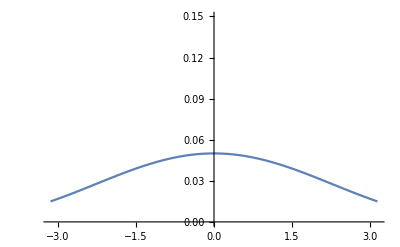

```mathematica
Plot[h[ξ,1],{ξ,-Pi,Pi},PlotRange->{0,0.15}]
```

```mathematica
h[Pi,1]
```

0.0149558

## Upper-bounding the Numerator

Let’s go back to the (ugly) numerator, and try to get an upper bound for that.

```mathematica
dFnum=Simplify[dFnum]
```

{0.06 Sin[ξ/2]-(4.16667 Sin[ξ/2])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2+(ⅇ^(20 t) t (800 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]-(400. Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (Cos[β0-ξ] (9.02778+1.67361 offset+(8.33333+2.16667 offset) Cos[ξ/2]+0.5 offset Cos[ξ])+4.16667 Sin[β0-ξ] Sin[ξ/2]) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2))/(160 √2 √(4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2)),(5 ⅇ^(20 t) t (-4 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (-Cos[β0]+(2 Cos[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]))/(4 √2 √(4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2))}

Note the presence of lowerBoundQty in the derivative for the “numerator”, as we would expect given the structure of that function. So let’s first get rid of that using the bound we just derived:

```mathematica
dFnum1=dFnum//.{Evaluate[lowerBoundQty[ξ,β0,offset]]->denLB}
```

{0.06 Sin[ξ/2]-(4.16667 Sin[ξ/2])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2+1/(160 √2 √denLB)ⅇ^(20 t) t (800 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]-(400. Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (Cos[β0-ξ] (9.02778+1.67361 offset+(8.33333+2.16667 offset) Cos[ξ/2]+0.5 offset Cos[ξ])+4.16667 Sin[β0-ξ] Sin[ξ/2]) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2),(5 ⅇ^(20 t) t (-4 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (-Cos[β0]+(2 Cos[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]))/(4 √2 √denLB)}

#### Deal with the first component:

SPLIT ON ADDITION

```mathematica
dFnum1Components=List@@dFnum1⟦1⟧
```

{0.06 Sin[ξ/2],-(4.16667 Sin[ξ/2])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2,1/(160 √2 √denLB)ⅇ^(20 t) t (800 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]-(400. Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (Cos[β0-ξ] (9.02778+1.67361 offset+(8.33333+2.16667 offset) Cos[ξ/2]+0.5 offset Cos[ξ])+4.16667 Sin[β0-ξ] Sin[ξ/2]) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2)}

The first two components are easily bounded as:

```mathematica
a1=dFnum1Components⟦1⟧/.Sin[ξ/2]->1
```

0.06

```mathematica
a2=Abs[dFnum1Components⟦2⟧/.{Sin[ξ/2]->1,Cos[ξ/2]->0}]
```

4.16667/Abs[8.33333+1.08333 offset]^2

Now we deal with the final component

SPLIT on PRODUCT

```mathematica
dFnum1Components⟦3⟧
```

1/(160 √2 √denLB)ⅇ^(20 t) t (800 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]-(400. Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (Cos[β0-ξ] (9.02778+1.67361 offset+(8.33333+2.16667 offset) Cos[ξ/2]+0.5 offset Cos[ξ])+4.16667 Sin[β0-ξ] Sin[ξ/2]) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2)

Capture the factor in front:

```mathematica
b3=Times@@((List@@dFnum1Components⟦3⟧)⟦;;-2⟧)
```

(ⅇ^(20 t) t)/(160 √2 √denLB)

Now split the

SPLIT ON ADDITION AGAIN

```mathematica
a3list=List@@Last[List@@dFnum1Components⟦3⟧]
```

{800 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]],-((400. Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (Cos[β0-ξ] (9.02778+1.67361 offset+(8.33333+2.16667 offset) Cos[ξ/2]+0.5 offset Cos[ξ])+4.16667 Sin[β0-ξ] Sin[ξ/2]) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2)}

```mathematica
Dimensions[a3list]
```

{2}

Now we will handle these terms manually:

```mathematica
a31=a3list⟦1⟧/.{Cos[β0-ξ]->1,Sin[β0-ξ]->1,Abs'->Sign}
```

800

```mathematica
a3list⟦2⟧
```

-((400. Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (Cos[β0-ξ] (9.02778+1.67361 offset+(8.33333+2.16667 offset) Cos[ξ/2]+0.5 offset Cos[ξ])+4.16667 Sin[β0-ξ] Sin[ξ/2]) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2)

```mathematica
a32=-a3list⟦2⟧/.{
Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]->(1+2/(offset+4/(0.52+0.48))),
Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]->1,
1/(8.333333333333334+1.0833333333333335 offset+1. offset Cos[ξ/2])^2->1/(8.333333333333334+1.0833333333333335 offset+1. offset *0)^2

}/.{
Cos[β0-ξ] ->1, Cos[ξ/2]->1, Cos[ξ]->1,Sin[β0-ξ] Sin[ξ/2]->1
}
```

(400. (21.5278+4.34028 offset) (1+2/(4.+offset)))/(8.33333+1.08333 offset)^2

```mathematica
comp1UB[denLB_,t_,offset_]:=Evaluate[(a1+a2+b3*a31+b3*a32)]
```

#### Deal with the second component:

```mathematica
dFnum1Components=List@@dFnum1⟦2⟧
```

{5/4,1/(√2),1/(√denLB),ⅇ^(20 t),t,-4 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (-Cos[β0]+(2 Cos[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]}

```mathematica
b1=Times@@(dFnum1Components⟦;;-2⟧)
```

(5 ⅇ^(20 t) t)/(4 √2 √denLB)

```mathematica
a1List=List@@dFnum1Components⟦-1⟧
```

{-4 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]],Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (-Cos[β0]+(2 Cos[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]}

```mathematica
a1=-a1List⟦1⟧/.{
Cos[β0-ξ]->1, Sin[β0-ξ] ->1,Abs'->Sign
}
```

4

```mathematica
a2=a1List⟦2⟧/.{
Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] ->(1+2/(offset+4/(0.52+0.48))),
(-Cos[β0]+(2 Cos[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))) ->(1+2/(offset+4/(0.52+0.48))),
Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]->1
}
```

(1+2/(4.+offset))^2

```mathematica
comp2UB[denLB_,t_,offset_]:=Evaluate[b1*(a1+a2)]
```

## Combined bound for the Implicit Function Derivative on D\S_offset

It is now easy to assemble the above bounds into a single, overall bound for the derivative of the function t̃[ξ,β_0] outside the set S_offset (we will use the Max-norm here because it makes choosing the grid easier):

```mathematica
dBound[Toffset_,offset_]:=1/fullDenomLB[Toffset,offset]*Max[comp1UB[denomLB[Toffset,offset],Toffset,offset],comp2UB[denomLB[Toffset,offset],Toffset,offset]]
```

This gives us the following (somewhat reasonable) bound for the Lipschitz constant of the implicit function t̃[ξ,β_0] outside the set S_offset:

```mathematica
Tmax[offs]
```

0.25

```mathematica
offs
```

1

```mathematica
dBound[Tmax[offs],offs]
```

1.0633×10^9

```mathematica
1/fullDenomLB[Tmax[offs],offs]
```

2480.87

```mathematica
dBound[0.275,8]
```

8862.16

## Combining this code to create a Python lookup table

```mathematica
calcTable=(
Append[#,
"lut"->ParallelTable[
Quiet@Block[{ξ=Min[-Pi+(ξidx-1)*(2*Pi)/#"xiPoints",Pi],
β=Min[-betaMax+(βidx-1)*(2*betaMax)/#"betaPoints",betaMax]},
t/.Flatten@NSolve[Sqrt[2]*Lh*Norm[f[ξ, β, #"offs"]]*t*Exp[Lf*t] == h[ξ,  #"offs"],t]
],
{ξidx,1,#"xiPoints"+2},
{βidx,1,#"betaPoints"+2}
]
]
)&;
resultAssign[x_]:={"time"->x⟦1⟧,"lut"->x⟦2⟧};
calcTableFindMinimum=(
Append[#,
resultAssign@AbsoluteTiming[ParallelTable[
Block[{blkSize={Min[10*#"groupSize",#"xiPoints"+1-ξidx],Min[#"groupSize",#"betaPoints"+1-βidx]}},
Quiet[
{
N@Min[-Pi+(ξidx-1)*(2*Pi)/#"xiPoints",Pi],
N@Min[-betaMax+(βidx-1)*(2*betaMax)/#"betaPoints",betaMax],
Min[Table[
Block[
{ξ=Min[-Pi+(ξidx+xiInnerIdx-1)*(2*Pi)/#"xiPoints",Pi],
β=Min[-betaMax+(βidx+betaInnerIdx-1)*(2*betaMax)/#"betaPoints",betaMax]},
FindArgMin[(Sqrt[2]*Lh*Norm[f[ξ, β, #"offs"]]*t*Exp[Lf*t] - h[ξ,  #"offs"])^2,{t,0.2}]
],
{xiInnerIdx,0,blkSize⟦1⟧},
{betaInnerIdx,0,blkSize⟦2⟧}
]]-#"eps"
}
]
]
,
{ξidx,1,#"xiPoints"+1,10*#"groupSize"},
{βidx,1,#"betaPoints"+1,#"groupSize"}
]]
]
)&;
```

Compiled version using FindMinimum (no faster)

```mathematica
mainFun=Compile[{{blkSize,_Integer,1},{ξidx,_Integer},{βidx,_Integer},{xiPoints,_Integer},{betaPoints,_Integer},{offs,_Real},{eps,_Real}},
Module[{x},
x=Table[FindArgMin[(Sqrt[2]*Lh*Norm[f[Min[-Pi+(ξidx+xiInnerIdx-1)*(2*Pi)/xiPoints,Pi], Min[-betaMax+(βidx+betaInnerIdx-1)*(2*betaMax)/betaPoints,betaMax], offs]]*t*Exp[Lf*t] - h[Min[-Pi+(ξidx+xiInnerIdx-1)*(2*Pi)/xiPoints,Pi],  offs])^2,{t,0.2}],
{xiInnerIdx,0,blkSize⟦1⟧},
{betaInnerIdx,0,blkSize⟦2⟧}
];
{
N@Min[-Pi+(ξidx-1)*(2*Pi)/xiPoints,Pi],
N@Min[-betaMax+(βidx-1)*(2*betaMax)/betaPoints,betaMax],
Min[x]-eps
}
],
{{x,_Real,3},{FindArgMin[_],_Real,1}}
];
mainFunString="mainFun=Compile[{{blkSize,_Integer,1},{ξidx,_Integer},{βidx,_Integer},{xiPoints,_Integer},{betaPoints,_Integer},{offs,_Real},{eps,_Real}},
Module[{x},
x=Table[FindArgMin[(Sqrt[2]*Lh*Norm[f[Min[-Pi+(ξidx+xiInnerIdx-1)*(2*Pi)/xiPoints,Pi], Min[-betaMax+(βidx+betaInnerIdx-1)*(2*betaMax)/betaPoints,betaMax], offs]]*t*Exp[Lf*t] - h[Min[-Pi+(ξidx+xiInnerIdx-1)*(2*Pi)/xiPoints,Pi],  offs])^2,{t,0.2}],
{xiInnerIdx,0,blkSize⟦1⟧},
{betaInnerIdx,0,blkSize⟦2⟧}
];
{
N@Min[-Pi+(ξidx-1)*(2*Pi)/xiPoints,Pi],
N@Min[-betaMax+(βidx-1)*(2*betaMax)/betaPoints,betaMax],
Min[x]-eps
}
],
{{x,_Real,3},{FindArgMin[_],_Real,1}}
];";
ToExpression[mainFunString];
ParallelEvaluate[ToExpression[mainFunString];];
resultAssign[x_]:={"time"->x⟦1⟧,"lut"->x⟦2⟧};
calcTableFindMinimumCompiled=(
Append[#,
resultAssign@AbsoluteTiming[ParallelTable[
Block[{blkSize={Min[10*#"groupSize",#"xiPoints"+1-ξidx],Min[#"groupSize",#"betaPoints"+1-βidx]}},
mainFun[blkSize,ξidx,βidx,#"xiPoints",#"betaPoints",#"offs",#"eps"]
]
,
{ξidx,1,#"xiPoints"+1,10*#"groupSize"},
{βidx,1,#"betaPoints"+1,#"groupSize"}
]]
]
)&;
```

```mathematica
offsetList={1,2,4,6,8,16};
eps=0.01*ConstantArray[1,Length[offsetList]];
groupSize=10*ConstantArray[1,Length[offsetList]];
ToffsetInner={0.11,0.12,0.13,0.14,0.15,0.15};
ToffsetOuter=ToffsetInner-0.01;
chFact=500; (* Should be 1 :-( *)
xiGridPoints=Ceiling[(2*Pi)*(dBound@@@({ToffsetInner,offsetList}ᵀ))/eps/chFact];
betaGridPoints=Ceiling[(2*betaMax)*(dBound@@@({ToffsetInner,offsetList}ᵀ))/eps/chFact];
tableParams=Association@@@((Thread/@{"offs"->offsetList,"Tinner"->ToffsetInner,"Touter"->ToffsetOuter,"xiPoints"->xiGridPoints,"betaPoints"->betaGridPoints,"eps"->eps,"groupSize"->groupSize})ᵀ);
luts=Table[Null,{Length[tableParams]}];
SetDirectory[NotebookDirectory[]];
DumpSave["runcontext.mx",{Lh,f,Lf,h,vmax,lr,sigma,rBar,rmin,betaMax,tableParams,calcTable,calcTableFindMinimum,calcTableFindMinimumCompiled,mainFunString,resultAssign,chFact}];
(*luts=calcTable/@tableParams;*)
betaGridPoints*xiGridPoints
```

{96697910,49133785,32348925,59526012,158513327,48621171}

```mathematica
idx=-1;
AbsoluteTiming[luts⟦idx⟧=calcTableFindMinimum[tableParams⟦idx⟧];]
```

```mathematica
luts⟦idx⟧["lut"]
```

{{{-3.14159,-0.463648,0.0193913},{-3.14159,-0.422798,0.0191761},{-3.14159,-0.381948,0.0189837},{-3.14159,-0.341098,0.0188138},{-3.14159,-0.300248,0.0186661},{-3.14159,-0.259398,0.0185404},{-3.14159,-0.218548,0.0184366},{-3.14159,-0.177698,0.0183544},{-3.14159,-0.136848,0.0182936},{-3.14159,-0.0959975,0.0182543},{-3.14159,-0.0551475,0.0182362},{-3.14159,-0.0142975,0.0182349},{-3.14159,0.0265525,0.0182394},{-3.14159,0.0674025,0.0182638},{-3.14159,0.108253,0.0183096},{-3.14159,0.149103,0.0183768},{-3.14159,0.189953,0.0184655},{-3.14159,0.230803,0.0185758},{-3.14159,0.271653,0.0187081},{-3.14159,0.312503,0.0188624},{-3.14159,0.353353,0.019039},{-3.14159,0.394203,0.0192383},{-3.14159,0.435053,0.0194604}},{{-2.73253,-0.463648,0.0294961},{-2.73253,-0.422798,0.0288354},{-2.73253,-0.381948,0.0282048},{-2.73253,-0.341098,0.0276056},{-2.73253,-0.300248,0.0270387},{-2.73253,-0.259398,0.0265042},{-2.73253,-0.218548,0.0260022},{-2.73253,-0.177698,0.0255325},{-2.73253,-0.136848,0.0250946},{-2.73253,-0.0959975,0.0246881},{-2.73253,-0.0551475,0.0243124},{-2.73253,-0.0142975,0.0239668},{-2.73253,0.0265525,0.0236508},{-2.73253,0.0674025,0.0233637},{-2.73253,0.108253,0.0231049},{-2.73253,0.149103,0.0228739},{-2.73253,0.189953,0.0226702},{-2.73253,0.230803,0.0224932},{-2.73253,0.271653,0.0223426},{-2.73253,0.312503,0.022218},{-2.73253,0.353353,0.0221192},{-2.73253,0.394203,0.0220457},{-2.73253,0.435053,0.0220094}},{{-2.32347,-0.463648,0.0475714},{-2.32347,-0.422798,0.0462783},{-2.32347,-0.381948,0.0449141},{-2.32347,-0.341098,0.0435244},{-2.32347,-0.300248,0.0421432},{-2.32347,-0.259398,0.0407944},{-2.32347,-0.218548,0.0394941},{-2.32347,-0.177698,0.0382522},{-2.32347,-0.136848,0.0370743},{-2.32347,-0.0959975,0.0359629},{-2.32347,-0.0551475,0.0349183},{-2.32347,-0.0142975,0.0339397},{-2.32347,0.0265525,0.033025},{-2.32347,0.0674025,0.0321722},{-2.32347,0.108253,0.0313784},{-2.32347,0.149103,0.0306411},{-2.32347,0.189953,0.0299576},{-2.32347,0.230803,0.0293253},{-2.32347,0.271653,0.0287417},{-2.32347,0.312503,0.0282045},{-2.32347,0.353353,0.0277116},{-2.32347,0.394203,0.027261},{-2.32347,0.435053,0.0269697}},{{-1.91441,-0.463648,0.0453821},{-1.91441,-0.422798,0.0472939},{-1.91441,-0.381948,0.0494371},{-1.91441,-0.341098,0.0518566},{-1.91441,-0.300248,0.0546115},{-1.91441,-0.259398,0.0577825},{-1.91441,-0.218548,0.061483},{-1.91441,-0.177698,0.0658792},{-1.91441,-0.136848,0.0641327},{-1.91441,-0.0959975,0.060808},{-1.91441,-0.0551475,0.057643},{-1.91441,-0.0142975,0.0547106},{-1.91441,0.0265525,0.0520294},{-1.91441,0.0674025,0.0495922},{-1.91441,0.108253,0.0473813},{-1.91441,0.149103,0.0453756},{-1.91441,0.189953,0.0435542},{-1.91441,0.230803,0.0418975},{-1.91441,0.271653,0.0403882},{-1.91441,0.312503,0.039011},{-1.91441,0.353353,0.0377527},{-1.91441,0.394203,0.0366017},{-1.91441,0.435053,0.0358544}},{{-1.50535,-0.463648,0.0374558},{-1.50535,-0.422798,0.0383001},{-1.50535,-0.381948,0.0392224},{-1.50535,-0.341098,0.0402297},{-1.50535,-0.300248,0.0413299},{-1.50535,-0.259398,0.0425324},{-1.50535,-0.218548,0.0438482},{-1.50535,-0.177698,0.0452899},{-1.50535,-0.136848,0.0468724},{-1.50535,-0.0959975,0.0486134},{-1.50535,-0.0551475,0.0505335},{-1.50535,-0.0142975,0.052657},{-1.50535,0.0265525,0.0550122},{-1.50535,0.0674025,0.0576312},{-1.50535,0.108253,0.060549},{-1.50535,0.149103,0.0637994},{-1.50535,0.189953,0.0674039},{-1.50535,0.230803,0.0713475},{-1.50535,0.271653,0.0669351},{-1.50535,0.312503,0.0623602},{-1.50535,0.353353,0.0585269},{-1.50535,0.394203,0.0552533},{-1.50535,0.435053,0.0532275}},{{-1.09628,-0.463648,0.0346404},{-1.09628,-0.422798,0.0349571},{-1.09628,-0.381948,0.0353148},{-1.09628,-0.341098,0.0357149},{-1.09628,-0.300248,0.036159},{-1.09628,-0.259398,0.0366489},{-1.09628,-0.218548,0.0371866},{-1.09628,-0.177698,0.0377744},{-1.09628,-0.136848,0.0384146},{-1.09628,-0.0959975,0.0391102},{-1.09628,-0.0551475,0.0398639},{-1.09628,-0.0142975,0.0406791},{-1.09628,0.0265525,0.0415591},{-1.09628,0.0674025,0.0425077},{-1.09628,0.108253,0.0435286},{-1.09628,0.149103,0.0446257},{-1.09628,0.189953,0.0458028},{-1.09628,0.230803,0.0470632},{-1.09628,0.271653,0.0484097},{-1.09628,0.312503,0.0498435},{-1.09628,0.353353,0.0513636},{-1.09628,0.394203,0.0529656},{-1.09628,0.435053,0.0546395}},{{-0.687223,-0.463648,0.0344866},{-0.687223,-0.422798,0.0346529},{-0.687223,-0.381948,0.0348066},{-0.687223,-0.341098,0.0349469},{-0.687223,-0.300248,0.0350731},{-0.687223,-0.259398,0.0351847},{-0.687223,-0.218548,0.0352836},{-0.687223,-0.177698,0.0354043},{-0.687223,-0.136848,0.0355584},{-0.687223,-0.0959975,0.0357462},{-0.687223,-0.0551475,0.0359683},{-0.687223,-0.0142975,0.0362252},{-0.687223,0.0265525,0.0365176},{-0.687223,0.0674025,0.0368463},{-0.687223,0.108253,0.0372122},{-0.687223,0.149103,0.0376161},{-0.687223,0.189953,0.038059},{-0.687223,0.230803,0.038542},{-0.687223,0.271653,0.0390662},{-0.687223,0.312503,0.0396328},{-0.687223,0.353353,0.0402428},{-0.687223,0.394203,0.0408973},{-0.687223,0.435053,0.0415974}},{{-0.278162,-0.463648,0.0351716},{-0.278162,-0.422798,0.0351288},{-0.278162,-0.381948,0.035118},{-0.278162,-0.341098,0.0351185},{-0.278162,-0.300248,0.0351409},{-0.278162,-0.259398,0.0351958},{-0.278162,-0.218548,0.0352811},{-0.278162,-0.177698,0.0353617},{-0.278162,-0.136848,0.0354263},{-0.278162,-0.0959975,0.0354743},{-0.278162,-0.0551475,0.0355057},{-0.278162,-0.0142975,0.0355176},{-0.278162,0.0265525,0.0354981},{-0.278162,0.0674025,0.0354617},{-0.278162,0.108253,0.0354318},{-0.278162,0.149103,0.0354287},{-0.278162,0.189953,0.0354338},{-0.278162,0.230803,0.0354677},{-0.278162,0.271653,0.0355337},{-0.278162,0.312503,0.0356318},{-0.278162,0.353353,0.0357624},{-0.278162,0.394203,0.0359257},{-0.278162,0.435053,0.0361221}},{{0.1309,-0.463648,0.0388946},{0.1309,-0.422798,0.0384152},{0.1309,-0.381948,0.0379745},{0.1309,-0.341098,0.0375716},{0.1309,-0.300248,0.0372055},{0.1309,-0.259398,0.0368756},{0.1309,-0.218548,0.0365811},{0.1309,-0.177698,0.0363212},{0.1309,-0.136848,0.0360955},{0.1309,-0.0959975,0.0359032},{0.1309,-0.0551475,0.0357441},{0.1309,-0.0142975,0.0356176},{0.1309,0.0265525,0.0355236},{0.1309,0.0674025,0.0354617},{0.1309,0.108253,0.0354086},{0.1309,0.149103,0.0353392},{0.1309,0.189953,0.0352538},{0.1309,0.230803,0.0351528},{0.1309,0.271653,0.0350367},{0.1309,0.312503,0.0349062},{0.1309,0.353353,0.0347619},{0.1309,0.394203,0.0346043},{0.1309,0.435053,0.0344905}},{{0.539961,-0.463648,0.0481956},{0.539961,-0.422798,0.0469878},{0.539961,-0.381948,0.0458448},{0.539961,-0.341098,0.0447673},{0.539961,-0.300248,0.0437547},{0.539961,-0.259398,0.0428057},{0.539961,-0.218548,0.0419183},{0.539961,-0.177698,0.0410905},{0.539961,-0.136848,0.0403199},{0.539961,-0.0959975,0.0396043},{0.539961,-0.0551475,0.0389414},{0.539961,-0.0142975,0.0383291},{0.539961,0.0265525,0.0377653},{0.539961,0.0674025,0.0372481},{0.539961,0.108253,0.0367757},{0.539961,0.149103,0.0363466},{0.539961,0.189953,0.0359592},{0.539961,0.230803,0.0356121},{0.539961,0.271653,0.0353043},{0.539961,0.312503,0.0350347},{0.539961,0.353353,0.0348023},{0.539961,0.394203,0.0346064},{0.539961,0.435053,0.0344866}},{{0.949023,-0.463648,0.0639218},{0.949023,-0.422798,0.0685476},{0.949023,-0.381948,0.0663106},{0.949023,-0.341098,0.0634718},{0.949023,-0.300248,0.0607443},{0.949023,-0.259398,0.0581809},{0.949023,-0.218548,0.0558012},{0.949023,-0.177698,0.0536069},{0.949023,-0.136848,0.0515901},{0.949023,-0.0959975,0.0497393},{0.949023,-0.0551475,0.0480413},{0.949023,-0.0142975,0.0464831},{0.949023,0.0265525,0.0450526},{0.949023,0.0674025,0.0437387},{0.949023,0.108253,0.0425311},{0.949023,0.149103,0.041421},{0.949023,0.189953,0.0404005},{0.949023,0.230803,0.0394623},{0.949023,0.271653,0.0386005},{0.949023,0.312503,0.0378094},{0.949023,0.353353,0.0370842},{0.949023,0.394203,0.0364206},{0.949023,0.435053,0.0359907}},{{1.35808,-0.463648,0.0406831},{1.35808,-0.422798,0.0421907},{1.35808,-0.381948,0.043856},{1.35808,-0.341098,0.0457018},{1.35808,-0.300248,0.0477557},{1.35808,-0.259398,0.0500516},{1.35808,-0.218548,0.052631},{1.35808,-0.177698,0.0555449},{1.35808,-0.136848,0.0588548},{1.35808,-0.0959975,0.0626312},{1.35808,-0.0551475,0.0669441},{1.35808,-0.0142975,0.0705667},{1.35808,0.0265525,0.0655964},{1.35808,0.0674025,0.0614476},{1.35808,0.108253,0.0579177},{1.35808,0.149103,0.0548693},{1.35808,0.189953,0.0522055},{1.35808,0.230803,0.0498555},{1.35808,0.271653,0.0477664},{1.35808,0.312503,0.0458976},{1.35808,0.353353,0.0442172},{1.35808,0.394203,0.0426999},{1.35808,0.435053,0.0417239}},{{1.76715,-0.463648,0.0295862},{1.76715,-0.422798,0.0301919},{1.76715,-0.381948,0.0308513},{1.76715,-0.341098,0.0315677},{1.76715,-0.300248,0.0323448},{1.76715,-0.259398,0.0331866},{1.76715,-0.218548,0.0340975},{1.76715,-0.177698,0.035082},{1.76715,-0.136848,0.0361452},{1.76715,-0.0959975,0.037292},{1.76715,-0.0551475,0.0385274},{1.76715,-0.0142975,0.0398558},{1.76715,0.0265525,0.0412806},{1.76715,0.0674025,0.0428032},{1.76715,0.108253,0.0444216},{1.76715,0.149103,0.0461281},{1.76715,0.189953,0.0479063},{1.76715,0.230803,0.0497264},{1.76715,0.271653,0.0515404},{1.76715,0.312503,0.0532764},{1.76715,0.353353,0.0548365},{1.76715,0.394203,0.0561014},{1.76715,0.435053,0.0548151}},{{2.17621,-0.463648,0.0234623},{2.17621,-0.422798,0.0236342},{2.17621,-0.381948,0.0238349},{2.17621,-0.341098,0.024065},{2.17621,-0.300248,0.0243251},{2.17621,-0.259398,0.0246161},{2.17621,-0.218548,0.0249386},{2.17621,-0.177698,0.0252935},{2.17621,-0.136848,0.0256819},{2.17621,-0.0959975,0.0261046},{2.17621,-0.0551475,0.0265627},{2.17621,-0.0142975,0.0270572},{2.17621,0.0265525,0.0275891},{2.17621,0.0674025,0.0281594},{2.17621,0.108253,0.0287689},{2.17621,0.149103,0.0294182},{2.17621,0.189953,0.0301076},{2.17621,0.230803,0.030837},{2.17621,0.271653,0.0316058},{2.17621,0.312503,0.0324124},{2.17621,0.353353,0.0332542},{2.17621,0.394203,0.0341272},{2.17621,0.435053,0.0350253}},{{2.58527,-0.463648,0.0200806},{2.58527,-0.422798,0.0199706},{2.58527,-0.381948,0.0198833},{2.58527,-0.341098,0.0198185},{2.58527,-0.300248,0.0197761},{2.58527,-0.259398,0.019756},{2.58527,-0.218548,0.0197542},{2.58527,-0.177698,0.0197582},{2.58527,-0.136848,0.0197827},{2.58527,-0.0959975,0.0198294},{2.58527,-0.0551475,0.0198986},{2.58527,-0.0142975,0.0199903},{2.58527,0.0265525,0.0201047},{2.58527,0.0674025,0.0202421},{2.58527,0.108253,0.0204025},{2.58527,0.149103,0.0205864},{2.58527,0.189953,0.020794},{2.58527,0.230803,0.0210256},{2.58527,0.271653,0.0212815},{2.58527,0.312503,0.021562},{2.58527,0.353353,0.0218675},{2.58527,0.394203,0.0221981},{2.58527,0.435053,0.0225542}},{{2.99433,-0.463648,0.0193913},{2.99433,-0.422798,0.0191761},{2.99433,-0.381948,0.0189837},{2.99433,-0.341098,0.0188138},{2.99433,-0.300248,0.0186661},{2.99433,-0.259398,0.0185404},{2.99433,-0.218548,0.0184366},{2.99433,-0.177698,0.0183544},{2.99433,-0.136848,0.0182936},{2.99433,-0.0959975,0.0182543},{2.99433,-0.0551475,0.0182362},{2.99433,-0.0142975,0.0182349},{2.99433,0.0265525,0.0182394},{2.99433,0.0674025,0.0182638},{2.99433,0.108253,0.0183096},{2.99433,0.149103,0.0183768},{2.99433,0.189953,0.0184655},{2.99433,0.230803,0.0185758},{2.99433,0.271653,0.0187081},{2.99433,0.312503,0.0188624},{2.99433,0.353353,0.019039},{2.99433,0.394203,0.0192383},{2.99433,0.435053,0.0194604}}}

```mathematica
mainFun
```

CompiledFunction[…]

```mathematica
luts⟦idx⟧["lut"]
```

{{Null[{100,10},1,1,1536,227,16,0.01],Null[{100,10},1,11,1536,227,16,0.01],Null[{100,10},1,21,1536,227,16,0.01],Null[{100,10},1,31,1536,227,16,0.01],Null[{100,10},1,41,1536,227,16,0.01],Null[{100,10},1,51,1536,227,16,0.01],Null[{100,10},1,61,1536,227,16,0.01],Null[{100,10},1,71,1536,227,16,0.01],Null[{100,10},1,81,1536,227,16,0.01],Null[{100,10},1,91,1536,227,16,0.01],Null[{100,10},1,101,1536,227,16,0.01],Null[{100,10},1,111,1536,227,16,0.01],Null[{100,10},1,121,1536,227,16,0.01],Null[{100,10},1,131,1536,227,16,0.01],Null[{100,10},1,141,1536,227,16,0.01],Null[{100,10},1,151,1536,227,16,0.01],Null[{100,10},1,161,1536,227,16,0.01],Null[{100,10},1,171,1536,227,16,0.01],Null[{100,10},1,181,1536,227,16,0.01],Null[{100,10},1,191,1536,227,16,0.01],Null[{100,10},1,201,1536,227,16,0.01],Null[{100,10},1,211,1536,227,16,0.01],Null[{100,7},1,221,1536,227,16,0.01]},{Null[{100,10},101,1,1536,227,16,0.01],Null[{100,10},101,11,1536,227,16,0.01],Null[{100,10},101,21,1536,227,16,0.01],Null[{100,10},101,31,1536,227,16,0.01],Null[{100,10},101,41,1536,227,16,0.01],Null[{100,10},101,51,1536,227,16,0.01],Null[{100,10},101,61,1536,227,16,0.01],Null[{100,10},101,71,1536,227,16,0.01],Null[{100,10},101,81,1536,227,16,0.01],Null[{100,10},101,91,1536,227,16,0.01],Null[{100,10},101,101,1536,227,16,0.01],Null[{100,10},101,111,1536,227,16,0.01],Null[{100,10},101,121,1536,227,16,0.01],Null[{100,10},101,131,1536,227,16,0.01],Null[{100,10},101,141,1536,227,16,0.01],Null[{100,10},101,151,1536,227,16,0.01],Null[{100,10},101,161,1536,227,16,0.01],Null[{100,10},101,171,1536,227,16,0.01],Null[{100,10},101,181,1536,227,16,0.01],Null[{100,10},101,191,1536,227,16,0.01],Null[{100,10},101,201,1536,227,16,0.01],Null[{100,10},101,211,1536,227,16,0.01],Null[{100,7},101,221,1536,227,16,0.01]},{Null[{100,10},201,1,1536,227,16,0.01],Null[{100,10},201,11,1536,227,16,0.01],Null[{100,10},201,21,1536,227,16,0.01],Null[{100,10},201,31,1536,227,16,0.01],Null[{100,10},201,41,1536,227,16,0.01],Null[{100,10},201,51,1536,227,16,0.01],Null[{100,10},201,61,1536,227,16,0.01],Null[{100,10},201,71,1536,227,16,0.01],Null[{100,10},201,81,1536,227,16,0.01],Null[{100,10},201,91,1536,227,16,0.01],Null[{100,10},201,101,1536,227,16,0.01],Null[{100,10},201,111,1536,227,16,0.01],Null[{100,10},201,121,1536,227,16,0.01],Null[{100,10},201,131,1536,227,16,0.01],Null[{100,10},201,141,1536,227,16,0.01],Null[{100,10},201,151,1536,227,16,0.01],Null[{100,10},201,161,1536,227,16,0.01],Null[{100,10},201,171,1536,227,16,0.01],Null[{100,10},201,181,1536,227,16,0.01],Null[{100,10},201,191,1536,227,16,0.01],Null[{100,10},201,201,1536,227,16,0.01],Null[{100,10},201,211,1536,227,16,0.01],Null[{100,7},201,221,1536,227,16,0.01]},{Null[{100,10},301,1,1536,227,16,0.01],Null[{100,10},301,11,1536,227,16,0.01],Null[{100,10},301,21,1536,227,16,0.01],Null[{100,10},301,31,1536,227,16,0.01],Null[{100,10},301,41,1536,227,16,0.01],Null[{100,10},301,51,1536,227,16,0.01],Null[{100,10},301,61,1536,227,16,0.01],Null[{100,10},301,71,1536,227,16,0.01],Null[{100,10},301,81,1536,227,16,0.01],Null[{100,10},301,91,1536,227,16,0.01],Null[{100,10},301,101,1536,227,16,0.01],Null[{100,10},301,111,1536,227,16,0.01],Null[{100,10},301,121,1536,227,16,0.01],Null[{100,10},301,131,1536,227,16,0.01],Null[{100,10},301,141,1536,227,16,0.01],Null[{100,10},301,151,1536,227,16,0.01],Null[{100,10},301,161,1536,227,16,0.01],Null[{100,10},301,171,1536,227,16,0.01],Null[{100,10},301,181,1536,227,16,0.01],Null[{100,10},301,191,1536,227,16,0.01],Null[{100,10},301,201,1536,227,16,0.01],Null[{100,10},301,211,1536,227,16,0.01],Null[{100,7},301,221,1536,227,16,0.01]},{Null[{100,10},401,1,1536,227,16,0.01],Null[{100,10},401,11,1536,227,16,0.01],Null[{100,10},401,21,1536,227,16,0.01],Null[{100,10},401,31,1536,227,16,0.01],Null[{100,10},401,41,1536,227,16,0.01],Null[{100,10},401,51,1536,227,16,0.01],Null[{100,10},401,61,1536,227,16,0.01],Null[{100,10},401,71,1536,227,16,0.01],Null[{100,10},401,81,1536,227,16,0.01],Null[{100,10},401,91,1536,227,16,0.01],Null[{100,10},401,101,1536,227,16,0.01],Null[{100,10},401,111,1536,227,16,0.01],Null[{100,10},401,121,1536,227,16,0.01],Null[{100,10},401,131,1536,227,16,0.01],Null[{100,10},401,141,1536,227,16,0.01],Null[{100,10},401,151,1536,227,16,0.01],Null[{100,10},401,161,1536,227,16,0.01],Null[{100,10},401,171,1536,227,16,0.01],Null[{100,10},401,181,1536,227,16,0.01],Null[{100,10},401,191,1536,227,16,0.01],Null[{100,10},401,201,1536,227,16,0.01],Null[{100,10},401,211,1536,227,16,0.01],Null[{100,7},401,221,1536,227,16,0.01]},{Null[{100,10},501,1,1536,227,16,0.01],Null[{100,10},501,11,1536,227,16,0.01],Null[{100,10},501,21,1536,227,16,0.01],Null[{100,10},501,31,1536,227,16,0.01],Null[{100,10},501,41,1536,227,16,0.01],Null[{100,10},501,51,1536,227,16,0.01],Null[{100,10},501,61,1536,227,16,0.01],Null[{100,10},501,71,1536,227,16,0.01],Null[{100,10},501,81,1536,227,16,0.01],Null[{100,10},501,91,1536,227,16,0.01],Null[{100,10},501,101,1536,227,16,0.01],Null[{100,10},501,111,1536,227,16,0.01],Null[{100,10},501,121,1536,227,16,0.01],Null[{100,10},501,131,1536,227,16,0.01],Null[{100,10},501,141,1536,227,16,0.01],Null[{100,10},501,151,1536,227,16,0.01],Null[{100,10},501,161,1536,227,16,0.01],Null[{100,10},501,171,1536,227,16,0.01],Null[{100,10},501,181,1536,227,16,0.01],Null[{100,10},501,191,1536,227,16,0.01],Null[{100,10},501,201,1536,227,16,0.01],Null[{100,10},501,211,1536,227,16,0.01],Null[{100,7},501,221,1536,227,16,0.01]},{Null[{100,10},601,1,1536,227,16,0.01],Null[{100,10},601,11,1536,227,16,0.01],Null[{100,10},601,21,1536,227,16,0.01],Null[{100,10},601,31,1536,227,16,0.01],Null[{100,10},601,41,1536,227,16,0.01],Null[{100,10},601,51,1536,227,16,0.01],Null[{100,10},601,61,1536,227,16,0.01],Null[{100,10},601,71,1536,227,16,0.01],Null[{100,10},601,81,1536,227,16,0.01],Null[{100,10},601,91,1536,227,16,0.01],Null[{100,10},601,101,1536,227,16,0.01],Null[{100,10},601,111,1536,227,16,0.01],Null[{100,10},601,121,1536,227,16,0.01],Null[{100,10},601,131,1536,227,16,0.01],Null[{100,10},601,141,1536,227,16,0.01],Null[{100,10},601,151,1536,227,16,0.01],Null[{100,10},601,161,1536,227,16,0.01],Null[{100,10},601,171,1536,227,16,0.01],Null[{100,10},601,181,1536,227,16,0.01],Null[{100,10},601,191,1536,227,16,0.01],Null[{100,10},601,201,1536,227,16,0.01],Null[{100,10},601,211,1536,227,16,0.01],Null[{100,7},601,221,1536,227,16,0.01]},{Null[{100,10},701,1,1536,227,16,0.01],Null[{100,10},701,11,1536,227,16,0.01],Null[{100,10},701,21,1536,227,16,0.01],Null[{100,10},701,31,1536,227,16,0.01],Null[{100,10},701,41,1536,227,16,0.01],Null[{100,10},701,51,1536,227,16,0.01],Null[{100,10},701,61,1536,227,16,0.01],Null[{100,10},701,71,1536,227,16,0.01],Null[{100,10},701,81,1536,227,16,0.01],Null[{100,10},701,91,1536,227,16,0.01],Null[{100,10},701,101,1536,227,16,0.01],Null[{100,10},701,111,1536,227,16,0.01],Null[{100,10},701,121,1536,227,16,0.01],Null[{100,10},701,131,1536,227,16,0.01],Null[{100,10},701,141,1536,227,16,0.01],Null[{100,10},701,151,1536,227,16,0.01],Null[{100,10},701,161,1536,227,16,0.01],Null[{100,10},701,171,1536,227,16,0.01],Null[{100,10},701,181,1536,227,16,0.01],Null[{100,10},701,191,1536,227,16,0.01],Null[{100,10},701,201,1536,227,16,0.01],Null[{100,10},701,211,1536,227,16,0.01],Null[{100,7},701,221,1536,227,16,0.01]},{Null[{100,10},801,1,1536,227,16,0.01],Null[{100,10},801,11,1536,227,16,0.01],Null[{100,10},801,21,1536,227,16,0.01],Null[{100,10},801,31,1536,227,16,0.01],Null[{100,10},801,41,1536,227,16,0.01],Null[{100,10},801,51,1536,227,16,0.01],Null[{100,10},801,61,1536,227,16,0.01],Null[{100,10},801,71,1536,227,16,0.01],Null[{100,10},801,81,1536,227,16,0.01],Null[{100,10},801,91,1536,227,16,0.01],Null[{100,10},801,101,1536,227,16,0.01],Null[{100,10},801,111,1536,227,16,0.01],Null[{100,10},801,121,1536,227,16,0.01],Null[{100,10},801,131,1536,227,16,0.01],Null[{100,10},801,141,1536,227,16,0.01],Null[{100,10},801,151,1536,227,16,0.01],Null[{100,10},801,161,1536,227,16,0.01],Null[{100,10},801,171,1536,227,16,0.01],Null[{100,10},801,181,1536,227,16,0.01],Null[{100,10},801,191,1536,227,16,0.01],Null[{100,10},801,201,1536,227,16,0.01],Null[{100,10},801,211,1536,227,16,0.01],Null[{100,7},801,221,1536,227,16,0.01]},{Null[{100,10},901,1,1536,227,16,0.01],Null[{100,10},901,11,1536,227,16,0.01],Null[{100,10},901,21,1536,227,16,0.01],Null[{100,10},901,31,1536,227,16,0.01],Null[{100,10},901,41,1536,227,16,0.01],Null[{100,10},901,51,1536,227,16,0.01],Null[{100,10},901,61,1536,227,16,0.01],Null[{100,10},901,71,1536,227,16,0.01],Null[{100,10},901,81,1536,227,16,0.01],Null[{100,10},901,91,1536,227,16,0.01],Null[{100,10},901,101,1536,227,16,0.01],Null[{100,10},901,111,1536,227,16,0.01],Null[{100,10},901,121,1536,227,16,0.01],Null[{100,10},901,131,1536,227,16,0.01],Null[{100,10},901,141,1536,227,16,0.01],Null[{100,10},901,151,1536,227,16,0.01],Null[{100,10},901,161,1536,227,16,0.01],Null[{100,10},901,171,1536,227,16,0.01],Null[{100,10},901,181,1536,227,16,0.01],Null[{100,10},901,191,1536,227,16,0.01],Null[{100,10},901,201,1536,227,16,0.01],Null[{100,10},901,211,1536,227,16,0.01],Null[{100,7},901,221,1536,227,16,0.01]},{Null[{100,10},1001,1,1536,227,16,0.01],Null[{100,10},1001,11,1536,227,16,0.01],Null[{100,10},1001,21,1536,227,16,0.01],Null[{100,10},1001,31,1536,227,16,0.01],Null[{100,10},1001,41,1536,227,16,0.01],Null[{100,10},1001,51,1536,227,16,0.01],Null[{100,10},1001,61,1536,227,16,0.01],Null[{100,10},1001,71,1536,227,16,0.01],Null[{100,10},1001,81,1536,227,16,0.01],Null[{100,10},1001,91,1536,227,16,0.01],Null[{100,10},1001,101,1536,227,16,0.01],Null[{100,10},1001,111,1536,227,16,0.01],Null[{100,10},1001,121,1536,227,16,0.01],Null[{100,10},1001,131,1536,227,16,0.01],Null[{100,10},1001,141,1536,227,16,0.01],Null[{100,10},1001,151,1536,227,16,0.01],Null[{100,10},1001,161,1536,227,16,0.01],Null[{100,10},1001,171,1536,227,16,0.01],Null[{100,10},1001,181,1536,227,16,0.01],Null[{100,10},1001,191,1536,227,16,0.01],Null[{100,10},1001,201,1536,227,16,0.01],Null[{100,10},1001,211,1536,227,16,0.01],Null[{100,7},1001,221,1536,227,16,0.01]},{Null[{100,10},1101,1,1536,227,16,0.01],Null[{100,10},1101,11,1536,227,16,0.01],Null[{100,10},1101,21,1536,227,16,0.01],Null[{100,10},1101,31,1536,227,16,0.01],Null[{100,10},1101,41,1536,227,16,0.01],Null[{100,10},1101,51,1536,227,16,0.01],Null[{100,10},1101,61,1536,227,16,0.01],Null[{100,10},1101,71,1536,227,16,0.01],Null[{100,10},1101,81,1536,227,16,0.01],Null[{100,10},1101,91,1536,227,16,0.01],Null[{100,10},1101,101,1536,227,16,0.01],Null[{100,10},1101,111,1536,227,16,0.01],Null[{100,10},1101,121,1536,227,16,0.01],Null[{100,10},1101,131,1536,227,16,0.01],Null[{100,10},1101,141,1536,227,16,0.01],Null[{100,10},1101,151,1536,227,16,0.01],Null[{100,10},1101,161,1536,227,16,0.01],Null[{100,10},1101,171,1536,227,16,0.01],Null[{100,10},1101,181,1536,227,16,0.01],Null[{100,10},1101,191,1536,227,16,0.01],Null[{100,10},1101,201,1536,227,16,0.01],Null[{100,10},1101,211,1536,227,16,0.01],Null[{100,7},1101,221,1536,227,16,0.01]},{Null[{100,10},1201,1,1536,227,16,0.01],Null[{100,10},1201,11,1536,227,16,0.01],Null[{100,10},1201,21,1536,227,16,0.01],Null[{100,10},1201,31,1536,227,16,0.01],Null[{100,10},1201,41,1536,227,16,0.01],Null[{100,10},1201,51,1536,227,16,0.01],Null[{100,10},1201,61,1536,227,16,0.01],Null[{100,10},1201,71,1536,227,16,0.01],Null[{100,10},1201,81,1536,227,16,0.01],Null[{100,10},1201,91,1536,227,16,0.01],Null[{100,10},1201,101,1536,227,16,0.01],Null[{100,10},1201,111,1536,227,16,0.01],Null[{100,10},1201,121,1536,227,16,0.01],Null[{100,10},1201,131,1536,227,16,0.01],Null[{100,10},1201,141,1536,227,16,0.01],Null[{100,10},1201,151,1536,227,16,0.01],Null[{100,10},1201,161,1536,227,16,0.01],Null[{100,10},1201,171,1536,227,16,0.01],Null[{100,10},1201,181,1536,227,16,0.01],Null[{100,10},1201,191,1536,227,16,0.01],Null[{100,10},1201,201,1536,227,16,0.01],Null[{100,10},1201,211,1536,227,16,0.01],Null[{100,7},1201,221,1536,227,16,0.01]},{Null[{100,10},1301,1,1536,227,16,0.01],Null[{100,10},1301,11,1536,227,16,0.01],Null[{100,10},1301,21,1536,227,16,0.01],Null[{100,10},1301,31,1536,227,16,0.01],Null[{100,10},1301,41,1536,227,16,0.01],Null[{100,10},1301,51,1536,227,16,0.01],Null[{100,10},1301,61,1536,227,16,0.01],Null[{100,10},1301,71,1536,227,16,0.01],Null[{100,10},1301,81,1536,227,16,0.01],Null[{100,10},1301,91,1536,227,16,0.01],Null[{100,10},1301,101,1536,227,16,0.01],Null[{100,10},1301,111,1536,227,16,0.01],Null[{100,10},1301,121,1536,227,16,0.01],Null[{100,10},1301,131,1536,227,16,0.01],Null[{100,10},1301,141,1536,227,16,0.01],Null[{100,10},1301,151,1536,227,16,0.01],Null[{100,10},1301,161,1536,227,16,0.01],Null[{100,10},1301,171,1536,227,16,0.01],Null[{100,10},1301,181,1536,227,16,0.01],Null[{100,10},1301,191,1536,227,16,0.01],Null[{100,10},1301,201,1536,227,16,0.01],Null[{100,10},1301,211,1536,227,16,0.01],Null[{100,7},1301,221,1536,227,16,0.01]},{Null[{100,10},1401,1,1536,227,16,0.01],Null[{100,10},1401,11,1536,227,16,0.01],Null[{100,10},1401,21,1536,227,16,0.01],Null[{100,10},1401,31,1536,227,16,0.01],Null[{100,10},1401,41,1536,227,16,0.01],Null[{100,10},1401,51,1536,227,16,0.01],Null[{100,10},1401,61,1536,227,16,0.01],Null[{100,10},1401,71,1536,227,16,0.01],Null[{100,10},1401,81,1536,227,16,0.01],Null[{100,10},1401,91,1536,227,16,0.01],Null[{100,10},1401,101,1536,227,16,0.01],Null[{100,10},1401,111,1536,227,16,0.01],Null[{100,10},1401,121,1536,227,16,0.01],Null[{100,10},1401,131,1536,227,16,0.01],Null[{100,10},1401,141,1536,227,16,0.01],Null[{100,10},1401,151,1536,227,16,0.01],Null[{100,10},1401,161,1536,227,16,0.01],Null[{100,10},1401,171,1536,227,16,0.01],Null[{100,10},1401,181,1536,227,16,0.01],Null[{100,10},1401,191,1536,227,16,0.01],Null[{100,10},1401,201,1536,227,16,0.01],Null[{100,10},1401,211,1536,227,16,0.01],Null[{100,7},1401,221,1536,227,16,0.01]},{Null[{36,10},1501,1,1536,227,16,0.01],Null[{36,10},1501,11,1536,227,16,0.01],Null[{36,10},1501,21,1536,227,16,0.01],Null[{36,10},1501,31,1536,227,16,0.01],Null[{36,10},1501,41,1536,227,16,0.01],Null[{36,10},1501,51,1536,227,16,0.01],Null[{36,10},1501,61,1536,227,16,0.01],Null[{36,10},1501,71,1536,227,16,0.01],Null[{36,10},1501,81,1536,227,16,0.01],Null[{36,10},1501,91,1536,227,16,0.01],Null[{36,10},1501,101,1536,227,16,0.01],Null[{36,10},1501,111,1536,227,16,0.01],Null[{36,10},1501,121,1536,227,16,0.01],Null[{36,10},1501,131,1536,227,16,0.01],Null[{36,10},1501,141,1536,227,16,0.01],Null[{36,10},1501,151,1536,227,16,0.01],Null[{36,10},1501,161,1536,227,16,0.01],Null[{36,10},1501,171,1536,227,16,0.01],Null[{36,10},1501,181,1536,227,16,0.01],Null[{36,10},1501,191,1536,227,16,0.01],Null[{36,10},1501,201,1536,227,16,0.01],Null[{36,10},1501,211,1536,227,16,0.01],Null[{36,7},1501,221,1536,227,16,0.01]}}

```mathematica
luts⟦idx⟧["lut"]⟦1,;;,2⟧
```

{-0.463648,-0.422798,-0.381948,-0.341098,-0.300248,-0.259398,-0.218548,-0.177698,-0.136848,-0.0959975,-0.0551475,-0.0142975,0.0265525,0.0674025,0.108253,0.149103,0.189953,0.230803,0.271653,0.312503,0.353353,0.394203,0.435053}

```mathematica
luts⟦idx⟧["lut"]⟦;;,;;,3⟧
```

{{0.0193913,0.0191761,0.0189837,0.0188138,0.0186661,0.0185404,0.0184366,0.0183544,0.0182936,0.0182543,0.0182362,0.0182349,0.0182394,0.0182638,0.0183096,0.0183768,0.0184655,0.0185758,0.0187081,0.0188624,0.019039,0.0192383,0.0194604},{0.0294961,0.0288354,0.0282048,0.0276056,0.0270387,0.0265042,0.0260022,0.0255325,0.0250946,0.0246881,0.0243124,0.0239668,0.0236508,0.0233637,0.0231049,0.0228739,0.0226702,0.0224932,0.0223426,0.022218,0.0221192,0.0220457,0.0220094},{0.0475714,0.0462783,0.0449141,0.0435244,0.0421432,0.0407944,0.0394941,0.0382522,0.0370743,0.0359629,0.0349183,0.0339397,0.033025,0.0321722,0.0313784,0.0306411,0.0299576,0.0293253,0.0287417,0.0282045,0.0277116,0.027261,0.0269697},{0.0453821,0.0472939,0.0494371,0.0518566,0.0546115,0.0577825,0.061483,0.0658792,0.0641327,0.060808,0.057643,0.0547106,0.0520294,0.0495922,0.0473813,0.0453756,0.0435542,0.0418975,0.0403882,0.039011,0.0377527,0.0366017,0.0358544},{0.0374558,0.0383001,0.0392224,0.0402297,0.0413299,0.0425324,0.0438482,0.0452899,0.0468724,0.0486134,0.0505335,0.052657,0.0550122,0.0576312,0.060549,0.0637994,0.0674039,0.0713475,0.0669351,0.0623602,0.0585269,0.0552533,0.0532275},{0.0346404,0.0349571,0.0353148,0.0357149,0.036159,0.0366489,0.0371866,0.0377744,0.0384146,0.0391102,0.0398639,0.0406791,0.0415591,0.0425077,0.0435286,0.0446257,0.0458028,0.0470632,0.0484097,0.0498435,0.0513636,0.0529656,0.0546395},{0.0344866,0.0346529,0.0348066,0.0349469,0.0350731,0.0351847,0.0352836,0.0354043,0.0355584,0.0357462,0.0359683,0.0362252,0.0365176,0.0368463,0.0372122,0.0376161,0.038059,0.038542,0.0390662,0.0396328,0.0402428,0.0408973,0.0415974},{0.0351716,0.0351288,0.035118,0.0351185,0.0351409,0.0351958,0.0352811,0.0353617,0.0354263,0.0354743,0.0355057,0.0355176,0.0354981,0.0354617,0.0354318,0.0354287,0.0354338,0.0354677,0.0355337,0.0356318,0.0357624,0.0359257,0.0361221},{0.0388946,0.0384152,0.0379745,0.0375716,0.0372055,0.0368756,0.0365811,0.0363212,0.0360955,0.0359032,0.0357441,0.0356176,0.0355236,0.0354617,0.0354086,0.0353392,0.0352538,0.0351528,0.0350367,0.0349062,0.0347619,0.0346043,0.0344905},{0.0481956,0.0469878,0.0458448,0.0447673,0.0437547,0.0428057,0.0419183,0.0410905,0.0403199,0.0396043,0.0389414,0.0383291,0.0377653,0.0372481,0.0367757,0.0363466,0.0359592,0.0356121,0.0353043,0.0350347,0.0348023,0.0346064,0.0344866},{0.0639218,0.0685476,0.0663106,0.0634718,0.0607443,0.0581809,0.0558012,0.0536069,0.0515901,0.0497393,0.0480413,0.0464831,0.0450526,0.0437387,0.0425311,0.041421,0.0404005,0.0394623,0.0386005,0.0378094,0.0370842,0.0364206,0.0359907},{0.0406831,0.0421907,0.043856,0.0457018,0.0477557,0.0500516,0.052631,0.0555449,0.0588548,0.0626312,0.0669441,0.0705667,0.0655964,0.0614476,0.0579177,0.0548693,0.0522055,0.0498555,0.0477664,0.0458976,0.0442172,0.0426999,0.0417239},{0.0295862,0.0301919,0.0308513,0.0315677,0.0323448,0.0331866,0.0340975,0.035082,0.0361452,0.037292,0.0385274,0.0398558,0.0412806,0.0428032,0.0444216,0.0461281,0.0479063,0.0497264,0.0515404,0.0532764,0.0548365,0.0561014,0.0548151},{0.0234623,0.0236342,0.0238349,0.024065,0.0243251,0.0246161,0.0249386,0.0252935,0.0256819,0.0261046,0.0265627,0.0270572,0.0275891,0.0281594,0.0287689,0.0294182,0.0301076,0.030837,0.0316058,0.0324124,0.0332542,0.0341272,0.0350253},{0.0200806,0.0199706,0.0198833,0.0198185,0.0197761,0.019756,0.0197542,0.0197582,0.0197827,0.0198294,0.0198986,0.0199903,0.0201047,0.0202421,0.0204025,0.0205864,0.020794,0.0210256,0.0212815,0.021562,0.0218675,0.0221981,0.0225542},{0.0193913,0.0191761,0.0189837,0.0188138,0.0186661,0.0185404,0.0184366,0.0183544,0.0182936,0.0182543,0.0182362,0.0182349,0.0182394,0.0182638,0.0183096,0.0183768,0.0184655,0.0185758,0.0187081,0.0188624,0.019039,0.0192383,0.0194604}}

```mathematica
Dimensions[luts⟦idx⟧["lut"]]
```

{16,23,3}

```mathematica
Max[Abs[temp-luts⟦idx⟧["lut"]]]
```

6.85364×10^-9

```mathematica
xiGridPoints
```

{8669.89,6953.81,4759.,7299.44,5545.98,2421.81}

```mathematica
(dBound@@@({ToffsetInner,offsetList}ᵀ))
```

{68.9928,55.3366,37.8709,58.0871,44.1335,19.2721}

8.46514×10^10 MB

88.7474 MB

57.0917 MB

```mathematica
Association@@@((Thread/@{"offs"->offsetList,"Tinner"->ToffsetInner,"Touter"->ToffsetOuter,"xiPoints"->xiGridPoints,"betaPoints"->betaGridPoints})ᵀ)
```

{<|offs→5,Tinner→0.2,Touter→0.19,xiPoints→8669.89,betaPoints→1279.53|>,<|offs→6,Tinner→0.2,Touter→0.19,xiPoints→6953.81,betaPoints→1026.27|>,<|offs→8,Tinner→0.2,Touter→0.19,xiPoints→4759.,betaPoints→702.351|>,<|offs→10,Tinner→0.21,Touter→0.2,xiPoints→7299.44,betaPoints→1077.28|>,<|offs→12,Tinner→0.21,Touter→0.2,xiPoints→5545.98,betaPoints→818.496|>,<|offs→20,Tinner→0.21,Touter→0.2,xiPoints→2421.81,betaPoints→357.419|>}

```mathematica
AppendTo
```

AppendTo

```mathematica
t/.Flatten@NSolve[Sqrt[2]*Lh*Norm[f[Pi,Pi/3,5]]*t*Exp[Lf*t] == h[Pi,5],t]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

0.0248787

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

0.0248787

```mathematica
luts⟦idx⟧["lut"]⟦6,18⟧
```

{-1.09628,0.230803,0.0470632}

```mathematica
numPoints=80;
offs=16;
rng={{-1.0962849364089382,-0.6872233929727672},{0.23080255426031315,0.27165256386390846}};
data=Flatten[ParallelTable[
{xi,beta,First@FindArgMin[(Sqrt[2]*Lh*Norm[f[xi,beta,offs]]*t*Exp[Lf*t]-h[xi,offs])^2,{t,0.2}]-0.01},
{xi,rng⟦1,1⟧,rng⟦1,2⟧,(rng⟦1,2⟧-rng⟦1,1⟧)/numPoints},
{beta,rng⟦2,1⟧,rng⟦2,2⟧,(rng⟦2,2⟧-rng⟦2,1⟧)/(2*numPoints)}
],1];
ListPlot3D[
data,
AxesLabel->(Style[#,FontSize->16]&/@{"ξ","β","Δt"}),
PlotRange->{{-1.0962849364089382,-0.6872233929727672},{0.23080255426031315,0.27165256386390846},{0.047,0.06}}
]
```

-Graphics3D-

```mathematica
numPoints=80;
offs=16;
rng={{-Pi,Pi},{-betaMax,betaMax}};
data=Flatten[ParallelTable[
{xi,beta,t/.Flatten@Quiet@NSolve[Sqrt[2]*Lh*Norm[f[xi,beta,offs]]*t*Exp[Lf*t]==h[xi,offs],t]},
{xi,rng⟦1,1⟧,rng⟦1,2⟧,(rng⟦1,2⟧-rng⟦1,1⟧)/numPoints},
{beta,rng⟦2,1⟧,rng⟦2,2⟧,(rng⟦2,2⟧-rng⟦2,1⟧)/(2*numPoints)}
],1];
ListPlot3D[
data,
AxesLabel->(Style[#,FontSize->16]&/@{"ξ","β","Δt"}),
PlotRange->{0,0.19}
]
```

-Graphics3D-

```mathematica
FullDefinition[rmin]
```

rmin[xi_,off_]:=rBar/(sigma Cos[xi/2]+1-sigma)+off
 
rBar=4
 
sigma=0.48

```mathematica
rmin[-Pi,20]
```

27.6923